## Coverage over a nomal distribution Mary Burbage and Aaron Becker Lesson: use RevolutionPlot3D, not Plot3D, http://mathworld.wolfram.com/BivariateNormalDistribution.html

### Distribution after a random walk of length r~U[0,1] at angle θ~U[0,2π]. Unsure about this result

```mathematica
D[{√(x^2+y^2),ArcTan[y,x]},{{x,y}}]//MatrixForm
```

(x/(√(x^2+y^2)) | y/(√(x^2+y^2))
y/(x^2+y^2) | -x/(x^2+y^2))

```mathematica
FullSimplify[Det[D[{√(x^2+y^2),ArcTan[x,y]},{{x,y}}]]]
```

1/(√(x^2+y^2))

```mathematica
-1/(√(x^2+y^2))*1/(2π)
```

-1/(2 π √(x^2+y^2))

```mathematica
Plot3D[1/(2 π √(x^2+y^2)),{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y,z},x^2+y^2<1],PlotRange->{Automatic,Automatic,{0,1}}]
```

-Graphics3D-

```mathematica
TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}]
```

TransformedDistribution[{x1 Cos[x2],x1 Sin[x2]},{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,2 π}]}]

```mathematica
d10e5=RandomVariate[TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}],1000000];
Histogram3D[d10e5,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
Histogram3D[d10e5,50,PerformanceGoal->"Speed"]
```

-Graphics3D-

```mathematica
Histogram3D[RandomVariate[TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}],10000]]
```

-Graphics3D-

```mathematica
Clear[x,y];PDF[TransformedDistribution[{r Cos[θ],r Sin[θ]},{r\[Distributed]UniformDistribution[{0,1}],θ\[Distributed]UniformDistribution[{0,2π}]}],{x,y}]
```

PDF[TransformedDistribution[{x1 Cos[x2],x1 Sin[x2]},{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,2 π}]}],{x,y}]

```mathematica
Plot3D[PDF[TransformedDistribution[{x1 Cos[x2],x1 Sin[x2]},{x1\[Distributed]UniformDistribution[{0,1}],x2\[Distributed]UniformDistribution[{0,2 π}]}],{x,y}],{x,-3,3},{y,-3,3}]
```

$Aborted

### Plot3D

```mathematica
Normal2[x_,y_,σ_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2+y^2))
Normal2onepass[x_,y_,σ_,r_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2+y^2))If[x^2+y^2<r^2,.1,1]
```

```mathematica
Plot3D[Normal2[x,y,2],{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[Normal2onepass[x,y,2,3],{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

### RevolutionPlot3D

```mathematica
Normal2rev[x_,σ_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2))
Normal2revonepass[x_,σ_,r_]:=1/(2π σ)ⅇ^(-1/(2 σ^2)(x^2))If[x<r,.5,1]
```

```mathematica
RevolutionPlot3D[Normal2rev[x,2],{x,0,8},PlotRange->{{-5,5},{-5,5},All}]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[Normal2revonepass[x,2,3],{x,0,8},PlotRange->{{-5,5},{-5,5},All},PlotLabel->{"50% probability removed for r<2"}]
```

-Graphics3D-

### Let's assume the drone covers an area of size a every second, and that this area is cleared in concentric circles (a gross simplification).

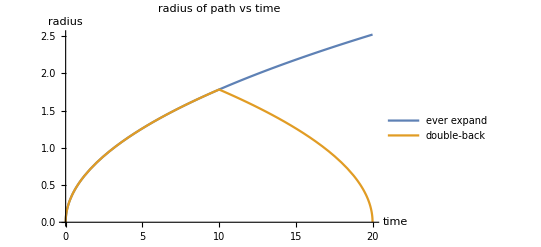

```mathematica
Plot[Evaluate[{√(a*t/π),If[t<10,√(a*t/π),(√(a (20-t)))/(√π)]}/.{a->1}],{t,0,20},PlotLabel-> "radius of path vs time",AxesLabel->{"time","radius"},PlotLegends->{"ever expand","double-back"}]
```

### What is r[t], the radius of the area cleared by a drone as a function of time? AreaCleared = a*t. AreaCleared = π r^2 Current Radius r[t] = √((a*t)/π) Current Radius path 2 r2[t] = √((10a-a*(t-10))/π)=(√(a (20-t)))/(√π)

```mathematica
(*Normal probability within radius of r*)
Clear[σ]
2π∫_0^r x(1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx
```

1-ⅇ^(-r^2/(2 σ^2))

```mathematica
(*Normal probability collected when spiralling out *)
Clear[T,a,σ,KillFrac,rt1,rt2]
KillFrac 2π∫_0^rt1[t] x(1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx
```

-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac

```mathematica
(*Normal probability collected when spiralling back in when t = T *)
Clear[T,a,σ,KillFrac,rt1,rt2]
FullSimplify[KillFrac 2π∫_0^rt1[T] x(1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx+KillFrac(1-KillFrac)2π∫_rt2[t,T]^rt1[T] x (1/(2π σ^2)ⅇ^(-1/(2 σ^2)(x^2)))ⅆx]
```

(1+ⅇ^(-rt1[T]^2/(2 σ^2)) (-2+KillFrac)-ⅇ^(-rt2[t,T]^2/(2 σ^2)) (-1+KillFrac)) KillFrac

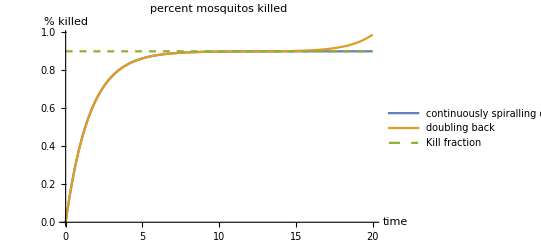

```mathematica
rt1[t_] := √(t/π);
rt2[t_,T_] := (√(2T-t))/(√π);
T = 10;
KillFrac = .9;
σ = 1/2;

Plot[{-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,If[t<T,-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,(1+ⅇ^(-rt1[T]^2/(2 σ^2)) (-2+KillFrac)-ⅇ^(-rt2[t,T]^2/(2 σ^2)) (-1+KillFrac)) KillFrac],KillFrac},{t,0,2T},PlotStyle->{Automatic,Automatic,Dashed},PlotLabel-> "percent mosquitos killed",AxesLabel->{"time","% killed"},PlotLegends->{"continuously spiralling out","doubling back","Kill fraction"},PlotRange->All]
```

```mathematica
Manipulate[Module[{rt1,rt2},rt1[t_] := √(t/π);
rt2[t_,T_] := (√(2T-t))/(√π);
Plot[{-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,If[t<T,-(-1+ⅇ^(-rt1[t]^2/(2 σ^2))) KillFrac,(1+ⅇ^(-rt1[T]^2/(2 σ^2)) (-2+KillFrac)-ⅇ^(-rt2[t,T]^2/(2 σ^2)) (-1+KillFrac)) KillFrac]},{t,0,2T},PlotLabel-> "percent mosquitos killed",AxesLabel->{"time","% killed"},

Epilog->{Line[{{T,0},{T,1}}]},PlotLegends->{"continuously spiralling out","doubling back"},PlotRange->All]],
{{T, 10},1/100,100},
{{KillFrac,.5},1/100,1} ,
{{σ , 2/3},1/100,10}]
```

## TODO : Simulate mosquitos always reforming normal dist,